```mathematica
vs = {0.5, 1, 2, 4};
legend = Table["v="<>ToString[v], {v, vs}]
```

{v=0.5,v=1,v=2,v=4}

```mathematica
FP = -D[p[x,t], t]+k*D[x*p[x, t], x]+(v/2)D[x*p[x, t], {x,2}]
```

-p^(0,1)[x,t]+k (p[x,t]+x p^(1,0)[x,t])+1/2 v (2 p^(1,0)[x,t]+x p^(2,0)[x,t])

```mathematica
p0= Table[N[PDF[NormalDistribution[10, v], x]],{v,vs}]
```

{0.797885 2.71828^(-2. (-10.+x)^2),0.398942 2.71828^(-0.5 (-10.+x)^2),0.199471 2.71828^(-0.125 (-10.+x)^2),0.0997356 2.71828^(-0.03125 (-10.+x)^2)}

```mathematica
bc =p[1, t]==0
```

p[1,t]==0

```mathematica
NDSolverParams[ic_, vr_] :=Module[{N},
N = NDSolve[{(FP/.{k->1, v->vr})==0,
 p[x, 0]==ic, 
p[1, t]==0, 
p[20,t]==0},
 p, {x, 1, 20}, {t, 0, 10}, 
MaxStepSize->0.01, 
Method->"MethodOfLines"];
Return[(p/.N[[1]])];
]
```

```mathematica
sols=MapThread[NDSolverParams, {p0, vs}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

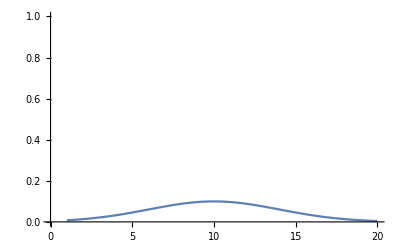

```mathematica
Plot[p0[[4]], {x, 1, 20}, PlotRange->{0,1}]
```

```mathematica
Manipulate[Plot[sols[[4]][x,t], {x, 1, 20}, PlotRange->{-0.01, 1}], {t, 0, 6}]
```

```mathematica
S[P_] := Integrate[P, {x, 1,20}] 
F[S_]:=D[-S, t]
```

```mathematica
Ss = Table[S[p[x,t]],{p, sols}]
Fs = Table[F[s], {s, Ss}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t]}

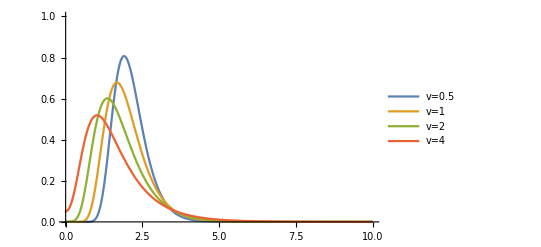

```mathematica
Plot[Fs, {t, 0, 10}, PlotRange->{0,1}, PlotLegends->legend]
```

```mathematica
NIntegrate[Fs[[2]], {t, 0, 600}]
```

0.999994